# Isotropic Schwarzschild center of mass

```mathematica
M=1;
x[r_, t_, p_]:=r Sin[t] Cos[p];
y[r_, t_, p_]:=r Sin[t] Sin[p];
z[r_, t_, p_]:=r Cos[t];
normal[r_,t_,p_]:= 1/r({{x[r,t,p]}, {y[r,t,p]}, {z[r,t,p]}});
```

```mathematica
zShift = 2;
shiftedR[r_, t_, p_] := √(x[r,t,p]^2+y[r,t,p]^2+(z[r,t,p]-zShift)^2);
shiftedRGradient[r_,t_,p_]:= ({{x[r,t,p]/shiftedR[r,t,p]}, {y[r,t,p]/shiftedR[r,t,p]}, {(z[r,t,p]-zShift)/shiftedR[r,t,p]}});
```

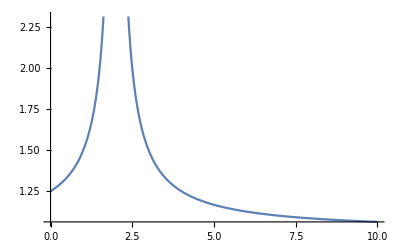

```mathematica
conformalFactor[r_,t_,p_] := 1 + M/(2 shiftedR[r,t,p]);
conformalFactorGradient[r_,t_,p_]:=- M/(2 shiftedR[r,t,p]^2) shiftedRGradient[r,t,p];
Plot[conformalFactor[r, 0, 0], {r, 0, 10}]
```

## Surface integral

```mathematica
surfaceIntegrand[r_, t_, p_]:= 3/(8 Pi M) conformalFactor[r,t,p]^4 normal[r,t,p];
surfaceIntegral[R_] := Integrate[surfaceIntegrand[R, t, p] R^2 Sin[t], {t, 0, Pi}, {p, 0, 2 Pi}] // Flatten
```

```mathematica
surfaceIntegral[3][[3]] // N
```

3.58189

```mathematica
For[i=1,i<8,i++,R=10^i;
	Print["R = ", R, ", surfIntZ = ", surfaceIntegral[R][[3]]// N];
]
```

R = 10, surfIntZ = 2.32082

R = 100, surfIntZ = 2.03016

R = 1000, surfIntZ = 2.003

R = 10000, surfIntZ = 2.0003

R = 100000, surfIntZ = 2.00003

R = 1000000, surfIntZ = 1.99976

R = 10000000, surfIntZ = 2.

## Volume integral

```mathematica
contractedConformalFactorGradient[r_,t_,p_]:=
	  conformalFactorGradient[r,t,p][[1]] normal[r,t,p][[1]] +
	conformalFactorGradient[r,t,p][[2]] normal[r,t,p][[2]] +
	conformalFactorGradient[r,t,p][[3]] normal[r,t,p][[3]];
volumeIntegrand[{r_, t_, p_}] := 3/(8 Pi M)(4 conformalFactor[r,t,p]^3 contractedConformalFactorGradient[r,t,p][[1]] normal[r,t,p]+2/r conformalFactor[r,t,p]^4 normal[r,t,p]) // Simplify // Flatten;
```

```mathematica
volumeIntegral[Rin_, Rout_] := NIntegrate[volumeIntegrand[{r, t, p}] r^2 Sin[t] ,{r, Rin, Rout}, {t, 0, Pi}, {p, 0, 2 Pi}];
```

```mathematica
For[i=1,i<=7,i++,R=10^i;
	volIntX = volumeIntegral[3, R][[1]] // N;
	volIntZ = volumeIntegral[3, R][[3]] // N;
	Print["R = ", R, ", volIntX = ", volIntX, ", volIntZ = ", volIntZ];
]
```

R = 10, volIntX = -1.00762×10^-11, volIntZ = -1.26106

R = 100, volIntX = 1.48982×10^-6, volIntZ = -1.55173

R = 1000, volIntX = -3.9937×10^-6, volIntZ = -1.57888

R = 10000, volIntX = -0.00371605, volIntZ = -1.59056

R = 100000, volIntX = 0.0147343, volIntZ = -1.35437

R = 1000000, volIntX = -0.00010635, volIntZ = -0.229992

R = 10000000, volIntX = -1.40108×10^6, volIntZ = -0.000679016

## Total integral tests

```mathematica
For[i=1,i<=4,i++,R=10^i;
	surfInt = surfaceIntegral[R][[3]] // N;
	volInt = volumeIntegral[R, 10^5][[3]] // N;
	totalInt = surfInt + volInt;
	Print["Rin = ", R, ", surfIntZ = ", surfInt, ", volIntZ = ", volInt, ", totalIntZ = ", totalInt];
]
```

Rin = 10, surfIntZ = 2.32082, volIntZ = -524.123, totalIntZ = -521.802

Rin = 100, surfIntZ = 2.03016, volIntZ = -0.0247282, totalIntZ = 2.00543

Rin = 1000, surfIntZ = 2.003, volIntZ = -0.00299232, totalIntZ = 2.00001

Rin = 10000, surfIntZ = 2.0003, volIntZ = -0.000269958, totalIntZ = 2.00003

```mathematica
For[i=1,i<=7,i++,R=10^i;
	surfInt = surfaceIntegral[3][[3]] // N ;
	volInt = volumeIntegral[3, R][[3]] // N;
	totalInt = surfInt + volInt;
	Print["Rout = ", R, ", surfIntZ = ", surfInt, ", volIntZ = ", volInt, ", totalIntZ = ", totalInt];
]
```

Rout = 10, surfIntZ = 3.58189, volIntZ = -1.26106, totalIntZ = 2.32082

Rout = 100, surfIntZ = 3.58189, volIntZ = -1.55173, totalIntZ = 2.03016

Rout = 1000, surfIntZ = 3.58189, volIntZ = -1.57888, totalIntZ = 2.003

Rout = 10000, surfIntZ = 3.58189, volIntZ = -1.59056, totalIntZ = 1.99132

Rout = 100000, surfIntZ = 3.58189, volIntZ = -1.35437, totalIntZ = 2.22752

Rout = 1000000, surfIntZ = 3.58189, volIntZ = -0.229992, totalIntZ = 3.35189

Rout = 10000000, surfIntZ = 3.58189, volIntZ = -0.000679016, totalIntZ = 3.58121